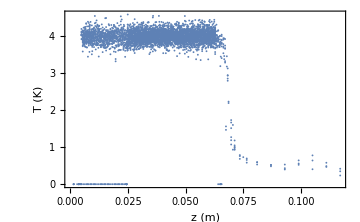
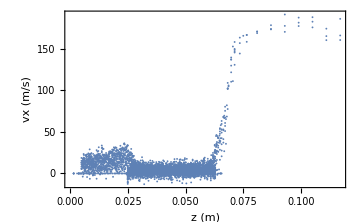
-Graphics--Graphics--Graphics-

```mathematica
d=Import["/home/cal/Documents/DSMC_Simulations/4_8_20_Yuiki_cell/flow_2.000_gap_0.000_len_0.000/data/DS2FF.500000.DAT","Table",HeaderLines->9];dcenter=Select[d,#[[2]]<0.004&];
x=dcenter[[;;,1]];
y=dcenter[[;;,2]];
T=dcenter[[;;,3]];
ρ=dcenter[[;;,4]];
vx=dcenter[[;;,6]];
Row[{ListPlot[Transpose@{x,T},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","T (K)",None,None},ImageSize->Medium],
ListPlot[Transpose@{x,ρ},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","ρ (1/m^3)",None,None},ImageSize->Medium],
ListPlot[Transpose@{x,vx},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","vx (m/s)",None,None},ImageSize->Medium]}]
```